```mathematica
fex[u_,urh_,ΔT_,urest_]:=-(u-urest)+ΔT Exp[(u-urh)/ΔT]
fquad[u_,a0_,uc_,urest_]:=a0(u-urest)(u-uc)
```

## Problem 1

### Part a

```mathematica
Solve[D[fex[u,urh,ΔT,urest],u]==0,u,Assumptions->{u∈Reals,urh ∈ Reals, ΔT ∈ Reals}]
```

{{u→urh}}

```mathematica
D[fex[u,urh,ΔT,urest],{u,2}]/.u->urh
```

1/ΔT

### Part b

```mathematica
minimum=(uc+urest)/2; curvature = 2 a0;
```

This implies 2 a0 = 1/ΔT and uc + urest = 2 urh if we match the parameters

### Part c

Let’s fix some values : τ=5, R I = 10, ΔT=1, urest = -1, urh = 3, which means a0 = 1/2 and uc = 7. Also t_refrac = 0.1. Also, given, u_fire = urh + 2 ΔT  and u_reset = urh - 2 ΔT

```mathematica
tr=0.1; ufire=5;ur=1;
```

```mathematica
Clear[GLIFexpeqns, u, t, GLIFexp]
GLIFexpeqns[t_] := {u'[t]==Piecewise[{{(-fex[u[t],3,1,-1]+10)/5, t>=treset[t]}, {0, True}}],WhenEvent[u[t]- ufire,{treset[t]->treset[t]+tr,u[t]->ur}],u[0]==-1,treset[0]==0};
GLIFexp = NDSolve[GLIFexpeqns[t],{u,treset},{t,0,10},DiscreteVariables->{treset}]
```

{{u→InterpolatingFunction[…],treset→InterpolatingFunction[…]}}

```mathematica
Clear[GLIFquadeqns, u, t, GLIFquad]
GLIFquadeqns[t_] := {u'[t]==Piecewise[{{(-fquad[u[t],1/2,7,-1]+10)/5, t>=treset[t]}, {0, True}}],WhenEvent[u[t]- ufire,{treset[t]->treset[t]+tr,u[t]->ur}],u[0]==-1,treset[0]==0};
GLIFquad= NDSolve[GLIFquadeqns[t],{u,treset},{t,0,10},DiscreteVariables->{treset}]
```

{{u→InterpolatingFunction[…],treset→InterpolatingFunction[…]}}

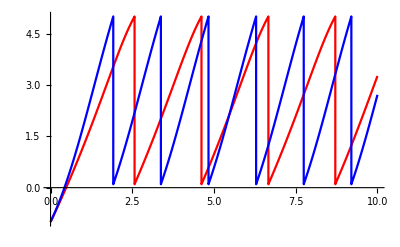

```mathematica
Show[{ListLinePlot[u/.First @GLIFexp,PlotRange->All,PlotStyle->{Red}],ListLinePlot[u/.First @GLIFquad,PlotRange->All,PlotStyle->{Blue}]}]
```